ps5. p1.

```mathematica
ClearAll[ AlGaN, permittivity, chi]
AlGaN = {
"omega_0"->1.921 10^14,
"omega_p"->3.328 10^14,
"gamma" -> 9.756 10^12
} ;

(* χ(ω) =Subscript[ω, p]^2/(Subscript[ω, 0]^2-ω^2+ j γ ω) *)
chi[omega_, medium_] := Module[{omegap, omega0, gamma}, {omegap, omega0, gamma} ={"omega_p", "omega_0", "gamma"} /. medium ;omegap^2/(omega0^2 - omega^2 + I gamma omega) 
]
```

a) Index of refraction

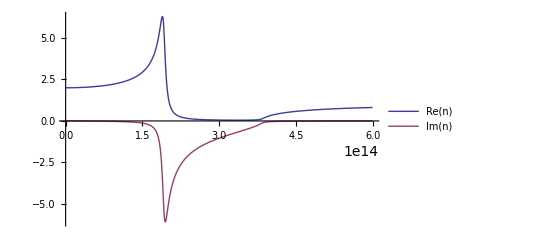

{p1IndexOfRefractionFig1.eps,p1IndexOfRefractionFig1pn.png}

```mathematica
p1a =Plot[{(1 +chi[omega, AlGaN] ) // Sqrt // Re, (1 +chi[omega, AlGaN] )// Sqrt // Im},{omega, 0, 6 10^14}, PlotLegends-> Placed[LineLegend[{"Re(n)", "Im(n)"}],{Right,Top}],
PlotRange -> Full]

peeters`exportForLatex["p1IndexOfRefractionFig1", p1a]
```

b) relative permittivity

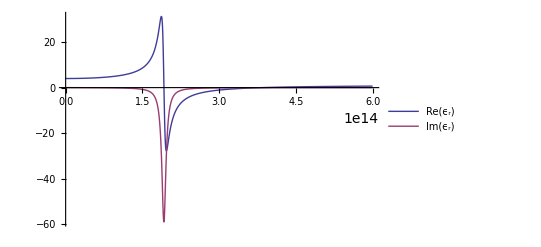

{p1EpsilonRFig2.eps,p1EpsilonRFig2pn.png}

```mathematica
p1b = Plot[{(1 +chi[omega, AlGaN] ) // Re, (1 +chi[omega, AlGaN] )// Im},{omega, 0, 6 10^14}, PlotLegends-> Placed[LineLegend[{"Re(ϵ_r)", "Im(ϵ_r)"}],{Right,Top}],
PlotRange -> Full]

peeters`exportForLatex["p1EpsilonRFig2", p1b]
```

ps5. p2.

```mathematica
ammonia1 = {
"omega_0"->2.4165825 10^15,
"omega_p"->10 10^9,
"gamma" -> 5 10^9
} ;

ammonia2 = {
"omega_0"->2.4166175 10^15,
"omega_p"->10 10^9,
"gamma" -> 5 10^9
} ;

omegac = 2.4166 10^15 ;
sevenGhz = 7 10^9 ;

(*toggled sign for active medium Subscript[ω, p,k]-> j Subscript[ω, p,k], or  Subscript[ω, p,k]^2->  -Subscript[ω, p,k]^2*)
permittivityAm[omega_] := 1 - chi[omega, ammonia1] - chi[omega, ammonia2] ;
nAm[nuDetuning_] := Sqrt[ permittivityAm[2 Pi nuDetuning + omegac]] ;
```

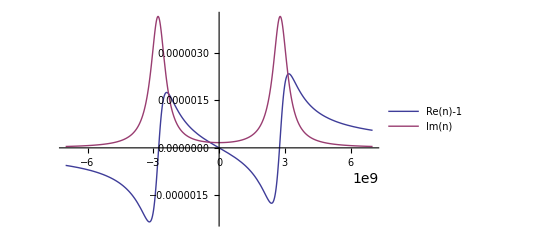

{p2nFig3.eps,p2nFig3pn.png}

```mathematica
p2n = Plot[{(nAm[nu]// Re) -1, (nAm[nu]// Im) -0},{nu, -sevenGhz, sevenGhz}, PlotLegends-> Placed[LineLegend[{"Re(n)-1", "Im(n)"}],{Right,Top}],
PlotRange -> Full]

peeters`exportForLatex["p2nFig3", p2]
```